```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/phy452-basicstatmech"]

fs=Style[#,FontSize->14]&;
```

### Problem 2.

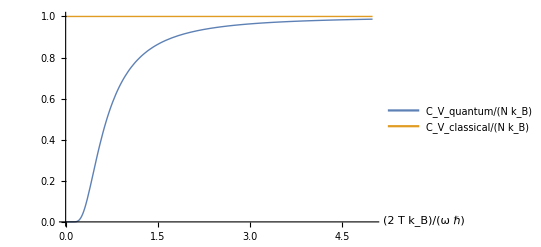

```mathematica
basicStatMechProblemSet5Problem2Fig1A = Plot[
{1/( t Sinh[1/t])^2,1},
 {t, 0, 5}, 
PlotRange -> Full,
PlotStyle->Thick,
AxesLabel -> {2 Subscript[k, B] T/(ℏ ω) //fs},
PlotLegends->Placed[{ "C_V_quantum/(N k_B)"//fs, "C_V_classical/(N k_B)"//fs}, Center]
]
```

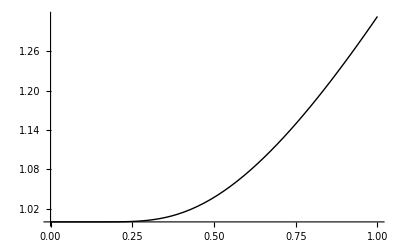

```mathematica
basicStatMechProblemSet5Problem2Fig2A = Plot[
Coth[1/t],
 {t, 0, 1}, 
PlotRange -> Full,
PlotStyle->{Black,Thick},
AxesLabel -> {
(*2 Subscript[k, B] T/(ℏ ω)//fs,
 2 U/(N ℏ ω)//fs*)
MaTeX["2 k_{\\mathrm{B}} T/{(\\hbar \\omega)}"],
MaTeX[" 2 U/{(N \\hbar \\omega)}"]
}
]
```

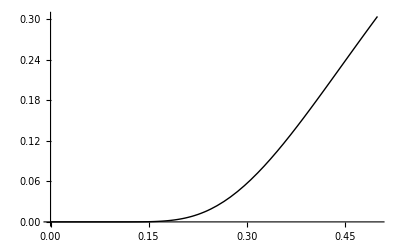

```mathematica
Plot[
1/(  t Sinh[1/t])^2,
 {t, 0, 0.5}, 
PlotRange -> Full,
PlotStyle->{Black,Thick},
AxesLabel -> {
(*2 Subscript[k, B] T/(ℏ ω) //fs, 
Subscript[C, V]/(N Subscript[k, B])//fs*)
MaTeX["2 k_{\\mathrm{B}} T / (\\hbar \\omega)"],
MaTeX["C_{\\mathrm{V}}/(N k_{\\mathrm{B}}) "]
}
]
```

```mathematica
FullSimplify[ Cosh[x]^2 + Sinh[x]^2]
```

Cosh[2 x]

```mathematica
peeters`exportForLatex["basicStatMechProblemSet5Problem2Fig2A",basicStatMechProblemSet5Problem2Fig2A]
```

{basicStatMechProblemSet5Problem2Fig2A.eps,basicStatMechProblemSet5Problem2Fig2Apn.png}

```mathematica
peeters`exportForLatex["basicStatMechProblemSet5Problem2Fig1A",basicStatMechProblemSet5Problem2Fig1A]
```

{basicStatMechProblemSet5Problem2Fig2A.eps,basicStatMechProblemSet5Problem2Fig2Apn.png}

{basicStatMechProblemSet5Problem2Fig1A.eps,basicStatMechProblemSet5Problem2Fig1Apn.png}